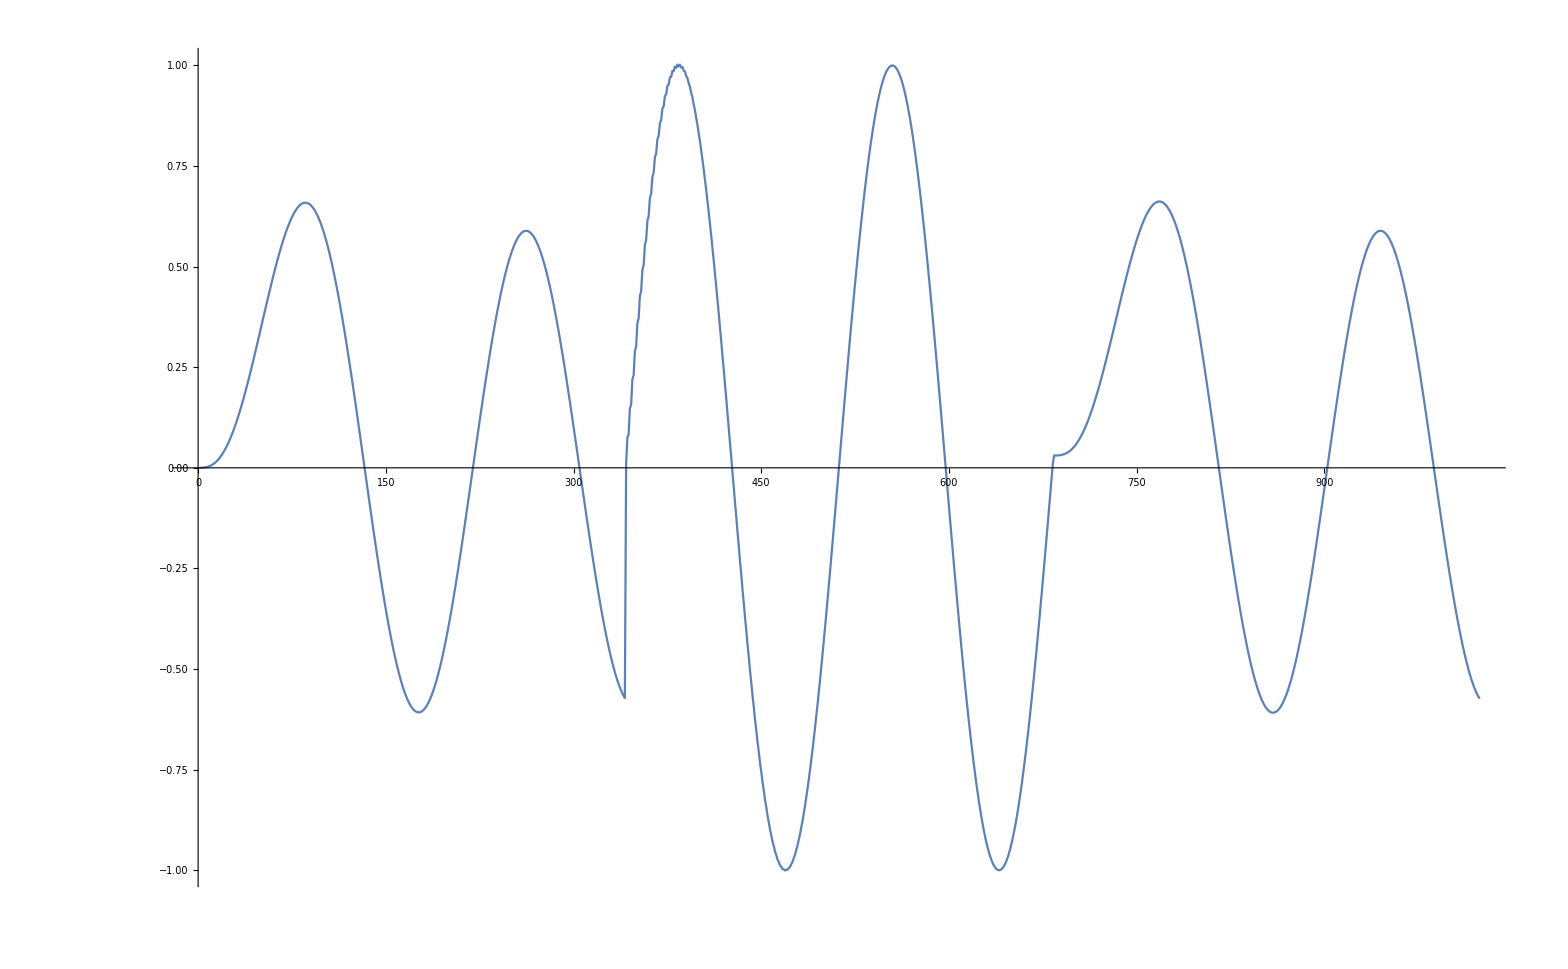

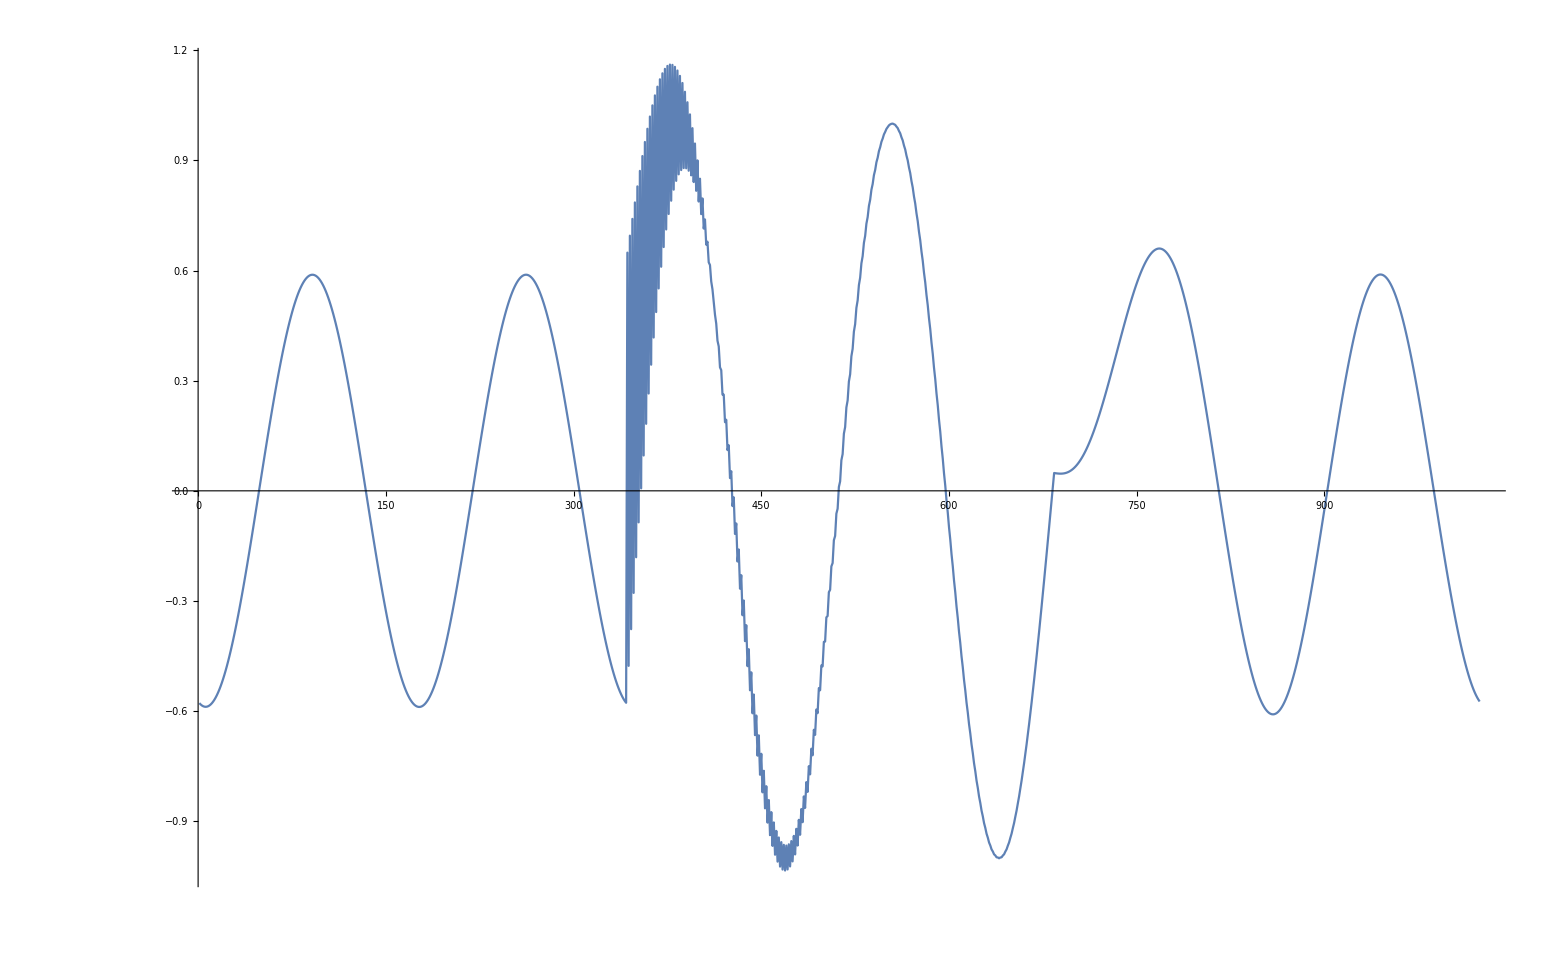

```mathematica
ic1 = 0;
ic2 = 0;
a1 = 0;
a2 = 0;
a3 = 0;

(* fc in [0,1]=[DC,Nyquist] *)
setFcAndQHard[fc_,Q_]:=Module[{g = Tan[π fc/2],k=1/Q},
a1 = 1/(1+g*(g+k));
a2 = g*a1;
a3 = g*a2;
]

setFcAndQSmooth[fc_,Q_,x_]:=Module[{a3Old,a2Old=a2,g = Tan[π fc/2],k=1/Q},
a3Old = a3;
a1 = 1/(1+g*(g+k));
a2 = g*a1;
a3 = g*a2;

ic1=(a2Old ic1)/a2;
ic2 = (-ic2+(a3Old ic2)-(a3Old *x)+(a3*x))/(-1+a3);
]

simperSVFLowpass[x_]:=Module[{v1, v2, v3},
v3= x - ic2;
v1 = a1 * ic1 + a2 * v3;
v2 = ic2 + a2 * ic1 + a3 * v3;
ic1 = 2 * v1 - ic1;
ic2 = 2 * v2 - ic2;
v2
]

testLength = 1024;
input = Sin[N[#]]&/@(6 π 2Range[testLength]/testLength);

setFcAndQHard[0.01,Sqrt[1/2]];
outputA = simperSVFLowpass[#]& /@ input[[1;;Round[testLength/3]]];
setFcAndQHard[0.99,Sqrt[1/2]];
outputB = simperSVFLowpass[#]& /@ input[[1+Round[testLength/3];;Round[2testLength/3]]];
setFcAndQHard[0.01,Sqrt[1/2]];
outputC = simperSVFLowpass[#]& /@ input[[1+Round[2testLength/3];;testLength]];
output = Join[outputA,outputB,outputC];
ListLinePlot[output]

setFcAndQSmooth[0.01,Sqrt[1/2],input[[1]]];
outputA = simperSVFLowpass[#]& /@ input[[1;;Round[testLength/3]]];
setFcAndQSmooth[0.99,Sqrt[1/2],input[[1+Round[testLength/3]]]];
outputB = simperSVFLowpass[#]& /@ input[[1+Round[testLength/3];;Round[2testLength/3]]];
setFcAndQSmooth[0.01,Sqrt[1/2],input[[1+Round[2testLength/3]]]];
outputC = simperSVFLowpass[#]& /@ input[[1+Round[2testLength/3];;testLength]];
output = Join[outputA,outputB,outputC];
ListLinePlot[output]
```

```mathematica
v3= x - ic2;
v1 = a1 * ic1 + a2 * v3;
v2 = ic2 + a2 * ic1 + a3 * v3;
(* Solve[ic2 + a2 * ic1 + a3 * v3==ic2n + a2n * ic1n + a3n * v3,?] *)
v2
```

a2 ic1+ic2+a3 (-ic2+x)

```mathematica
Solve[a2 ic1== a2n ic1n,ic1n]
Solve[ic2+a3(-ic2+x)==ic2n+a3n(-ic2n+x),ic2n]
```

{{ic1n→(a2 ic1)/a2n}}

{{ic2n→(-ic2+a3 ic2-a3 x+a3n x)/(-1+a3n)}}